# Data Resolution Mapping

BX Pan
2017.9.18

## Dataset

## CPC

```mathematica
SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation/global"];
CPC=FileNames["*.nc"];
%[[1;;3]]
```

{precip.1979.nc,precip.1980.nc,precip.1981.nc}

```mathematica
{cpcprecip,cpclat,cpclon}=Map[Import[CPC[[1]],{"Datasets",#}]&,{"precip","lat","lon"}];
cpcwoven=Table[Table[{cpclat[[i]],cpclon[[j]]},{j,Length[cpclon]}],{i,Length[cpclat]}];
```

```mathematica
Dimensions[cpcprecip]
```

{365,360,720}

## BoM

```mathematica
SetDirectory["/Users/lambda/Documents/Data/S2S/BoM"];
BoM=FileNames["*.nc"];
%[[1;;3]]
```

{BoM_1981-01-01.nc,BoM_1981-02-01.nc,BoM_1981-03-01.nc}

```mathematica
{bomprecip,bomlat,bomlon}=Map[Import[BoM[[1]],{"Datasets",#}]&,{"tp","latitude","longitude"}];
bomwoven=Table[Table[{bomlat[[i]],bomlon[[j]]},{j,Length[bomlon]}],{i,Length[bomlat]}];
```

Comparison

```mathematica
GraphicsRow[{ListLinePlot[{bomlat,cpclat},
			BaseStyle->15,
			PlotLabel->"Latitude\nBoM Interval="
					<>ToString[bomlat[[1]]-bomlat[[2]]]<>"\nCPC Interval="<>ToString[cpclat[[1]]-cpclat[[2]]],
			PlotLegends->{"BoM","CPC"},ImageSize->400],
			 ListLinePlot[{bomlon,cpclon},
			BaseStyle->15,
			PlotLabel->"Longitude\nBoM Interval="
					<>ToString[bomlon[[2]]-bomlon[[1]]]<>"\nCPC Interval="<>ToString[cpclon[[2]]-cpclon[[1]]],
			PlotLegends->{"BoM","CPC"},ImageSize->400]},ImageSize->1000]
```

-Graphics-

## Method

DownScaling

```mathematica
DownScale[data_,ratio_]:=Block[{convoluter},
	(* This Function performs spacial average downscaling of 2D data through uniform convolution   
	   ratio is kind like {5,4}*) 
	convoluter = Block[{net},
   	net = NetInitialize[ConvolutionLayer[1, ratio, "Stride" -> ratio, 
   						"Input" -> Flatten[{1, Dimensions[data]}]]];
       NetReplacePart[net, {"Weights" -> ConstantArray[1./(ratio/.List->Times), Flatten[{1, 1, ratio}]]}]];
    (convoluter@{data})[[1]]];
```

Cutting

#### Polygon

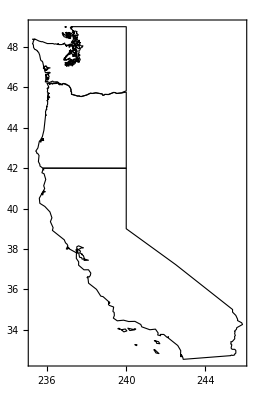

```mathematica
westconus=Block[{ow,ca},
	ow=Import["/Users/lambda/Documents/Data/GeoDivision/West Coast CONUS/oregonwashington.mx"];
	ca=Import["/Users/lambda/Documents/Data/GeoDivision/West Coast CONUS/california.mx"];
	Polygon[Flatten[{ow[[1]],ca[[1]]},1]]];
(*polygon in the form of {subpoly1,subpoly2,...},subpoly in th form of {{long1,lat1},{long2,lat2}...}*)
Graphics[{EdgeForm[Black],FaceForm[None],westconus},Frame->True]
```

#### Selection

```mathematica
DivisionSelect[polygons_,grids_]:=Block[{InOrOut},
	InOrOut[polygon_,point_]:=Block[{singletest},
		singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
		(Map[singletest,polygon])/.List->Or];
	Select[grids,InOrOut[polygons,Reverse[#]]&]]
```

```mathematica
bomgrids=DivisionSelect[westconus[[1]],Flatten[bomwoven,1]]
```

{{48.4123,240.},{45.9296,237.5},{45.9296,240.},{43.447,237.5},{43.447,240.},{40.9643,237.5},{40.9643,240.},{38.4817,237.5},{38.4817,240.},{35.999,240.},{35.999,242.5},{33.5163,242.5},{33.5163,245.}}

```mathematica
bomposition=Map[Position[bomwoven,#]&,bomgrids]
```

{{{17,97}},{{18,96}},{{18,97}},{{19,96}},{{19,97}},{{20,96}},{{20,97}},{{21,96}},{{21,97}},{{22,97}},{{22,98}},{{23,98}},{{23,99}}}

```mathematica
bomposition[[1,1,1]]
```

17

## Comparison

```mathematica
CPC[[3]]
cpc=Import["/Users/lambda/Documents/Data/CPC_Precipitation/global/"<>CPC[[3]],{"Datasets","precip"}];
```

precip.1981.nc

```mathematica
cpcCUT=Map[DownScale[#,{5,5}]&,cpc[[1;;62]]];
```

```mathematica
Dimensions[cpcCUT]
```

{62,72,144}

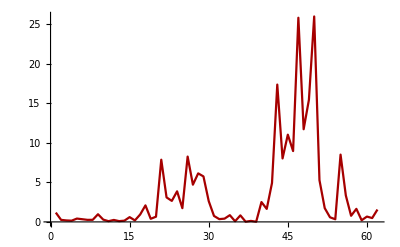
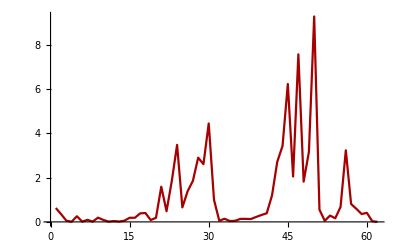
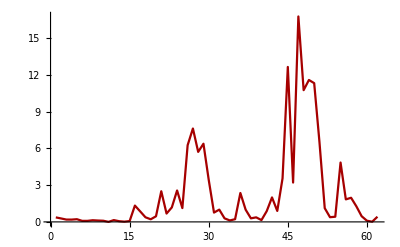
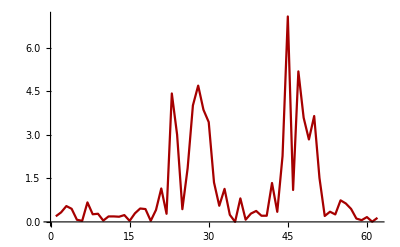
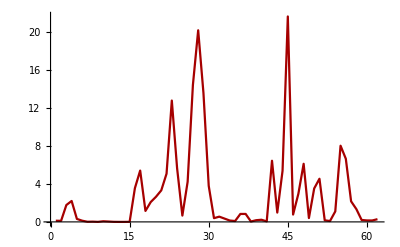
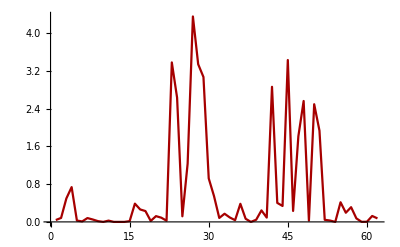
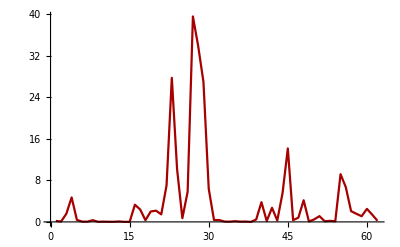
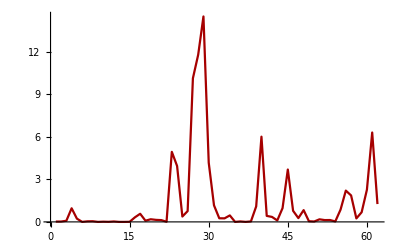
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ListLinePlot[cpcCUT[[;;,#[[1,1]],#[[1,2]]]],PlotRange->Full]&,bomposition]
```

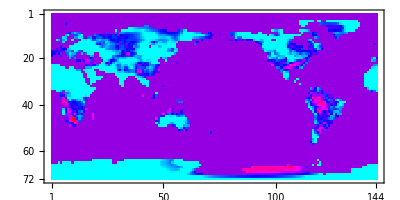

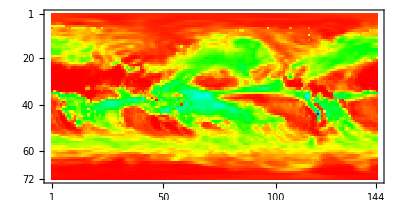
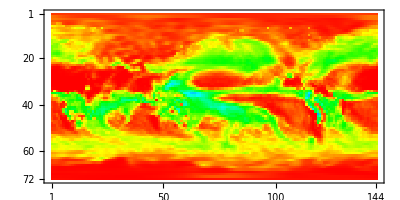
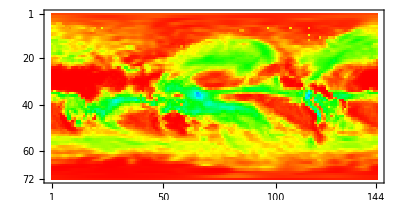
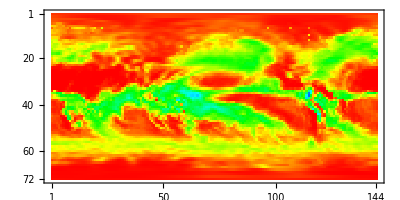
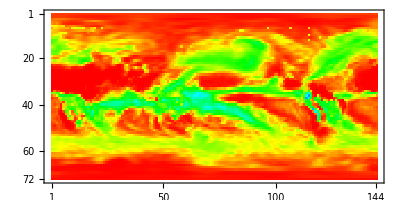

```mathematica
day=60;
MatrixPlot[cpcCUT[[day,;;,;;]],
	ColorFunction->Hue,
	PlotRange->{0.00,Max[cpcCUT]}]
	
Table[MatrixPlot[bom[[day,i,;;,;;]],
	ColorFunction->Hue,
	ColorFunction->Hue],{i,5}]
```

```mathematica
BoM[[1]]
bom=Import["/Users/lambda/Documents/Data/S2S/BoM/"<>BoM[[1]],{"Datasets","tp"}];
```

BoM_1981-01-01.nc

```mathematica
Dimensions[bom]
```

{62,32,72,144}

```mathematica
MinMax[bom[[1,1,;;,;;]]]
```

{-32766,-29926}

```mathematica
test=cpcCUT[[1,;;,;;]];
```

```mathematica
test=Replace[test, n_?(#<0&) -> 0, {2}];
```

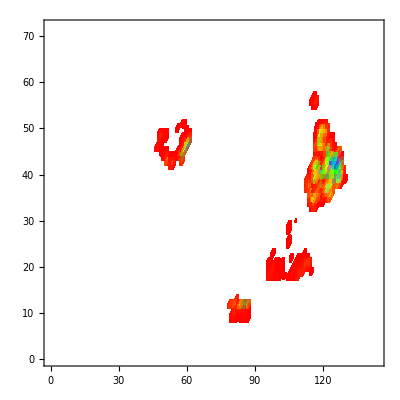

```mathematica
ListDensityPlot[test,ColorFunction->Hue,PlotRange->{0.001,Max[test]}]
```

```mathematica
Dimensions[bom]
```

{62,32,72,144}

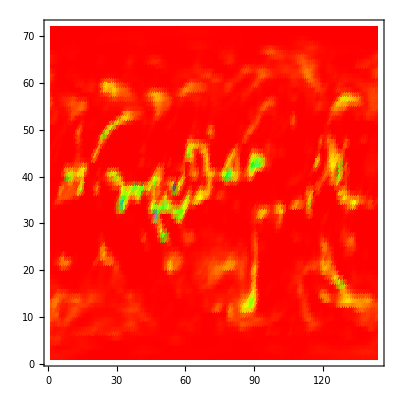
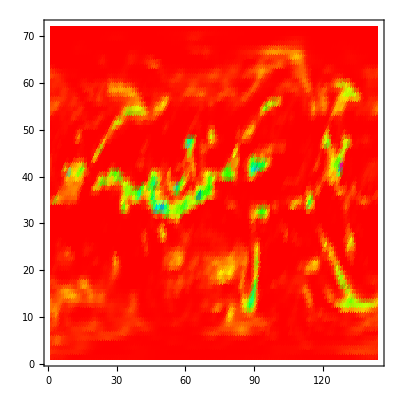
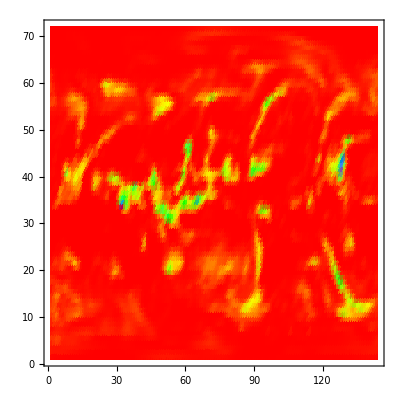
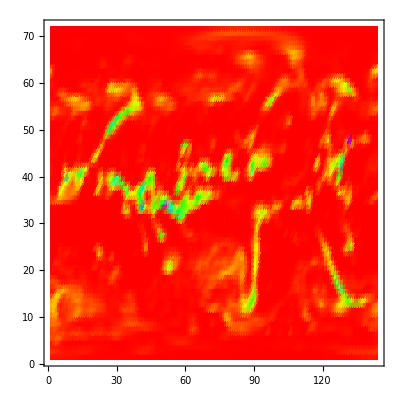
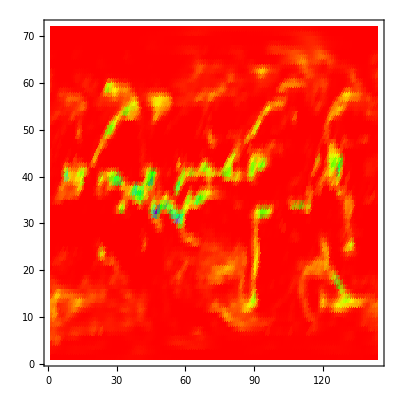
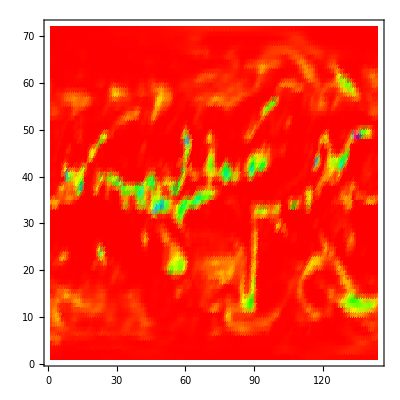
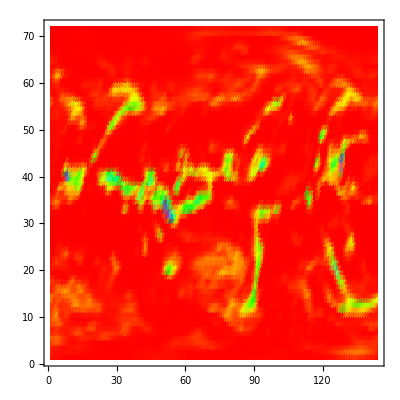
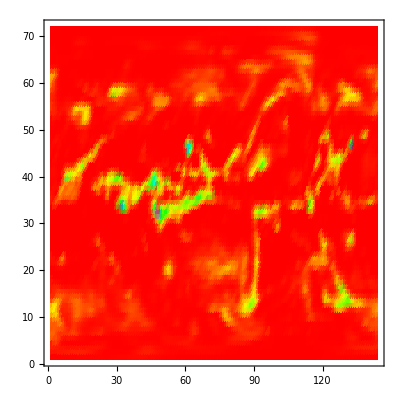

```mathematica
Table[ListDensityPlot[bom[[1,i,;;,;;]],ColorFunction->Hue,PlotRange->Full],{i,10}]
```